### Definitions for dynamics

```mathematica
(* Parameters *)
```

```mathematica
ParaDecayDelta[param_]:=param[[1]]; (* delta=0.02 *)
ParaDeathAdult[param_]:=param[[2]];(* uA=0.001 *)
ParaDeathJuvBase[param_]:=param[[3]]; (* uJ=0.001 *)
ParaDeathJuvEnv[param_]:=param[[4]];  (* uE=0.005 *)
ParaDeathJuvK[param_]:=param[[5]]; (* K=1 *)
```

```mathematica
defpara={0.02,0.001,0.001,0.005,1};
```

```mathematica
WinterSurvivalAdult[B_]:=sigmaA*B/(kA+B);
WinterSurvivalJuvenile[B_]:=sigmaJ*B/(kJ+B);
```

```mathematica
WinterSurvivalJuvenile[B_]:=sigmaJ*B/(kJ+B);
```

```mathematica
Snow[Env_,t_,param_]:=Env*Exp[-ParaDecayDelta[param]*t];
```

```mathematica
JuvenileDeath[Env_,param_]:=(ParaDeathJuvBase[param]+ParaDeathJuvEnv[param]*(Env/(ParaDeathJuvK[param]+Env)));
```

```mathematica
Adults[A_,t_,param_]:=A*Exp[-ParaDeathAdult[param]*t];
```

```mathematica
SeasonStartDY[A_,tau_,param_]:=NDSolve[{R'[t]==r*R[t](1-R[t]/Kr)-aA*Adults[A,t,param]*R[t],R[0]==Rini,BA'[t]==wA*aA*R[t]-betaA*BA[t],BA[0]==0},{R[t],BA[t]},{t,0,tau}][[1]]
```

```mathematica
SeasonStart[A_,tau_,param_]:=Module[{DYratk,koe},
DYratk=SeasonStartDY[A,tau,param];
({Adults[A,tau,param],BA[t],R[t]} /.  DYratk) /. t->tau]
```

```mathematica
SeasonEndDY[A_,tau_,Env_,{Amid_,BAmid_,Rmid_},param_]:=NDSolve[{R'[t]==r*R[t](1-R[t]/Kr)-(aA*Adults[A,t,param]+aJ*J[t])*R[t],R[tau]==Rmid,BA'[t]==wA*aA*R[t]-betaA*BA[t],BA[tau]==BAmid,J'[t]==-JuvenileDeath[Snow[Env,t,param],param]*J[t],J[tau]==alpha*Amid,BJ'[t]==wJ*aJ*R[t]-betaJ*BJ[t],BJ[tau]==0},{R[t],BA[t],J[t],BJ[t]},{t,tau,seasonT}][[1]]
```

```mathematica
SeasonEnd[A_,tau_,Env_,{Amid_,BAmid_,Rmid_},param_]:=Module[{DYratk,koe},
DYratk=SeasonEndDY[A,tau,Env,{Amid,BAmid,Rmid},param];
({Adults[A,t,param],BA[t],R[t],J[t],BJ[t]} /.  DYratk) /. t->seasonT]
```

```mathematica
DoStep[A_,tau_,Env_,param_]:=Module[{alku,Aend,BAend,Rend,Jend,BJend},
alku=SeasonStart[A,tau,param];
{Aend,BAend,Rend,Jend,BJend}=SeasonEnd[A,tau,Env,alku,param];
Aend*WinterSurvivalAdult[BAend]+Jend*WinterSurvivalJuvenile[BJend]
]
```

```mathematica
DoStepPrint[A_,tau_,Env_,param_]:=Module[{alku,Aend,BAend,Rend,Jend,BJend,currsnow,jdeath,Asurv,Jsurv},
alku=SeasonStart[A,tau,param];
currsnow=Snow[Env,tau,param];
jdeath=JuvenileDeath[currsnow,param];
Print["Snow ",currsnow," at time ",tau," => mortality ",jdeath];
Print["  Adults:",alku[[1]]," Pile ",alku[[2]]];
{Aend,BAend,Rend,Jend,BJend}=SeasonEnd[A,tau,Env,alku,param];
currsnow=Snow[Env,seasonT,param];
jdeath=JuvenileDeath[currsnow,param];
Print["Snow ",currsnow," at time ",seasonT," => mortality ",jdeath];
Asurv=WinterSurvivalAdult[BAend];
Print["Adults ",Aend, " Pile:",BAend , " survival: ",Asurv];
Jsurv=WinterSurvivalJuvenile[BJend];
Print["Juveniles ",Jend, " Pile:",BJend , " survival: ",Jsurv];
Print["Resource. R(0)=",Rini," ,R(tau)=",Last[alku]," R(end)=",Rend];
Aend*WinterSurvivalAdult[BAend]+Jend*WinterSurvivalJuvenile[BJend]
]
```

### Finding equilibria

```mathematica
(* If Mathematica tries to calculate with negative  A-values *)
RsearchCondition[A_?NumberQ,tau_,Env_,param_]:=If[A≤0,2-A,DoStep[A,tau,Env,param]/A];
```

```mathematica
PopuEquilibrium[tau_,Env_,param_]:=A /. FindRoot[RsearchCondition[A,tau,Env,param]==1,{A,0.01,0.2}]
```

### Definitions for gradient

```mathematica
deri=Simplify[D[sigmaJ*B/(kJ+B),B]]
```

(kJ sigmaJ)/(B+kJ)^2

```mathematica
deri/WinterSurvivalJuvenile[B]
```

kJ/(B (B+kJ))

```mathematica
WinterSurvivalJuvenileDeri[B_]:=(kJ sigmaJ)/(B+kJ)^2;
```

```mathematica
WinterSurvivalJuvenileDeriRelative[B_]:=kJ/(B (B+kJ));
```

```mathematica
PileAmountDeri[tau_ ,Rcurrent_]:=-Exp[-betaJ*(seasonT-tau)]*wJ*aJ*Rcurrent
```

```mathematica
GradientFullStep[{tau_,A_,Env_},param_]:=Module[{Amid,BAmid,Rmid,Aend,BAend,Rend,Jend,BJend,currsnow,jdeath,Asurv,Jsurv,deathDiff,BJderi,BsurvDeri,Bgrad,Mnumer,Mdenom,Multi,Astep},
{Amid,BAmid,Rmid}=SeasonStart[A,tau,param];
currsnow=Snow[Env,tau,param];
jdeath=JuvenileDeath[currsnow,param];
deathDiff=jdeath-ParaDeathAdult[param];
BJderi=PileAmountDeri[tau,Rmid];
(* Print["Snow ",currsnow," at time ",tau," => mortality ",jdeath]; *)
{Aend,BAend,Rend,Jend,BJend}=SeasonEnd[A,tau,Env,{Amid,BAmid,Rmid},param];
Asurv=WinterSurvivalAdult[BAend];
Jsurv=WinterSurvivalJuvenile[BJend];
Astep=Aend*Asurv+Jend*Jsurv;
BsurvDeri=WinterSurvivalJuvenileDeriRelative[BJend];
Bgrad=BJderi*BsurvDeri;
Mnumer=(Jend*Jsurv/A);
Mdenom=Mnumer+Aend*Asurv/A;
Multi=Mnumer/Mdenom;
{(deathDiff+Bgrad)*Multi,Astep}]
```

```mathematica
GradientDoStep[{tau_,A_,Env_},param_]:=GradientFullStep[{tau,A,Env},param][[1]]
```

```mathematica
GradientRandomStep[{grad_,A_},tau_,{EnvAver_,EnvDev_},param_]:=Module[{EnvR},
EnvR=EnvAver+(RandomReal[]-1/2)*EnvDev;
GradientFullStep[{tau,A,EnvR},param]
]
```

```mathematica
GradientThresholdRandomStep[{grad_,A_},threshold_,{EnvAver_,EnvDev_},param_]:=Module[{EnvR,tau,tauderi,delta,taugrad},
EnvR=EnvAver+(RandomReal[]-1/2)*EnvDev;
delta=ParaDecayDelta[param];
If[EnvR<threshold,tau=0;tauderi=0,tau=-(1/delta)*Log[threshold/EnvR];tauderi=-1/(delta*threshold)];
taugrad=GradientFullStep[{tau,A,EnvR},param];
{taugrad[[1]]*tauderi,taugrad[[2]]}
]
```

```mathematica
GradientRandomFinder[tau_,{EnvAver_,EnvDev_},{searchstep_,averstep_},param_]:=Module[{eqA,searchini,gradlist},
eqA=PopuEquilibrium[tau,EnvAver,param];
searchini=Nest[GradientRandomStep[#,tau,{EnvAver,EnvDev},param]&,{0,eqA},searchstep];
gradlist=NestList[GradientRandomStep[#,tau,{EnvAver,EnvDev},param]&,{0,eqA},averstep];
Mean[Map[First,gradlist]]]
```

```mathematica
GradientFinder[{tau_?NumberQ,Env_},param_]:=Module[{eqA},
eqA=PopuEquilibrium[tau,Env,param];
GradientDoStep[{tau,eqA,Env},param]]
```

```mathematica
GradientThresholdRandomFinder[threshold_,{EnvAver_,EnvDev_},{searchstep_,averstep_},param_]:=Module[{eqA,searchini,gradlist,tau,delta,temp},
delta=ParaDecayDelta[param];
If[EnvAver<threshold,tau=0,tau=-(1/delta)*Log[threshold/EnvAver]];
eqA=PopuEquilibrium[tau,EnvAver,param];
temp=PrintTemporary["Threshold ",threshold, " tau=",tau," Adults=",eqA, " Dev=",EnvDev]; 
searchini=Nest[GradientThresholdRandomStep[#,threshold,{EnvAver,EnvDev},param]&,{0,eqA},searchstep];
gradlist=NestList[GradientThresholdRandomStep[#,threshold,{EnvAver,EnvDev},param]&,{0,eqA},averstep];
NotebookDelete[temp];
Mean[Map[First,gradlist]]]
```

### Finding singular strategies

```mathematica
SingularTime[Env_,param_]:=strat /. FindRoot[GradientFinder[{strat,Env},param]==0,{strat,seasonT/2}]
```

```mathematica
RandSingularSearch[{Slow_,Shigh_,Scount_},{EnvAver_,EnvDev_},{searchstep_,averstep_},param_,plotting_]:=Module[{GradData,fitfunction,sing,singtemp,searchmid},
GradData=Table[{tau,GradientRandomFinder[tau,{EnvAver,EnvDev},{searchstep,averstep},param]},{tau,Slow,Shigh,(Shigh-Slow)/Scount}];
fitfunction=Fit[GradData,{1,x,x^2},x];
singtemp=x/.Solve[fitfunction==0,x];
searchmid=(Shigh+Slow)/2;
sing=Sort[singtemp,Abs[#1-searchmid]<Abs[#2-searchmid]&][[1]];
If[plotting>0,Print[Plot[fitfunction,{x,Slow,Shigh},Epilog->{{Red,Line[GradData]},{Line[{{sing,-1},{sing,1}}]}}]]
];
sing
]
```

```mathematica
RandSingularThresholdSearch[{Slow_,Shigh_,Scount_},{EnvAver_,EnvDev_},{searchstep_,averstep_},param_,plotting_]:=Module[{GradData,fitfunction,sing,singtemp,searchmid},
GradData=Table[{threshold,GradientThresholdRandomFinder[threshold,{EnvAver,EnvDev},{searchstep,averstep},param]},{threshold,Slow,Shigh,(Shigh-Slow)/Scount}];
fitfunction=Fit[GradData,{1,x,x^2},x];
singtemp=x/.Solve[fitfunction==0,x];
searchmid=(Shigh+Slow)/2;
sing=Sort[singtemp,Abs[#1-searchmid]<Abs[#2-searchmid]&][[1]];
If[plotting>0,Print[Plot[fitfunction,{x,Slow,Shigh},Epilog->{{Red,Line[GradData],PointSize[0.005],Map[Point,GradData]},{Line[{{sing,-1},{sing,1}}]}}]]
];
sing
]
```

### Effect of small variance

```mathematica
GradientDeri[{tau_,A_,Env_},param_,printing_]:=Module[{Amid,BAmid,Rmid,Aend,BAend,Rend,Jend,BJend,currsnow,jdeath,Asurv,Jsurv,deathDiff,BJderi,BsurvDeri,Bgrad,Mnumer,Mdenom,Multi,Astep,derifact,K},
{Amid,BAmid,Rmid}=SeasonStart[A,tau,param];
currsnow=Snow[Env,tau,param];
jdeath=JuvenileDeath[currsnow,param];
deathDiff=jdeath-ParaDeathAdult[param];
BJderi=PileAmountDeri[tau,Rmid];
(* Print["Snow ",currsnow," at time ",tau," => mortality ",jdeath]; *)
{Aend,BAend,Rend,Jend,BJend}=SeasonEnd[A,tau,Env,{Amid,BAmid,Rmid},param];
Asurv=WinterSurvivalAdult[BAend];
Jsurv=WinterSurvivalJuvenile[BJend];
Astep=Aend*Asurv+Jend*Jsurv;
BsurvDeri=WinterSurvivalJuvenileDeriRelative[BJend];
Bgrad=BJderi*BsurvDeri;
Mnumer=(Jend*Jsurv/A);
Mdenom=Mnumer+Aend*Asurv/A;
Multi=Mnumer/Mdenom;
If[printing>1,Print["RJ/(RJ+RA)=",Multi]];
K=ParaDeathJuvK[param];
If[printing>1,Print["Current snow=",currsnow, ", K=",K]];
derifact=-2*ParaDeathJuvEnv[param]*K*Exp[-ParaDecayDelta[param]*tau*2]/(K+currsnow)^3;
Multi*derifact]
```

```mathematica
SensitivityAnalysis[Env_,param_,printing_]:=Module[{sing,popu,grder,GrStratList,grfit,stratder,singder},
sing=SingularTime[Env,param];
popu=PopuEquilibrium[sing,Env,param];
grder=GradientDeri[{sing,popu,Env},param,printing];
If[printing>1,Print["Gradient derivative wrt environment",grder]];
GrStratList=Table[{sing+taudelta,GradientFinder[{sing+taudelta,Env},param]},{taudelta,-2,2,0.5}];
grfit=Fit[GrStratList,{1,x,x^2},x];
stratder=D[grfit,x]/. x->sing;
If[printing>2,Print[Plot[grfit,{x,sing-2,sing+2},Epilog->Map[Point,GrStratList]]]];
If[printing>1,Print["Gradient derivative wrt strategy",stratder]];
singder=-grder/stratder;
If[printing>0,Print[{sing,popu,singder}]];
{sing,popu,singder}
]
```

### Parameters

```mathematica
(* Snow *)
(* delta=0.02; *) EnvIniNormal=18;
(* Death-related *)
(* uA=0.001;uJ=0.001;uE=0.005;K=1; *)
(* Resource growth *)
r=0.044;Kr=150;
(* resource use *) aA=3;aJ=3;wA=0.33;wJ=0.33;
(* Haypile wither*) betaA=0.0015;betaJ=0.0015;
(* Reproduction *) alpha=1.5; 
(* Winter survival *) sigmaA=0.9;kA=2500;sigmaJ=0.9;kJ=2500;
```

```mathematica
(* Time *) seasonT=170;
(* Initial resource *) Rini=3;
```

### Plotting definitions

```mathematica
Koord[lista_]:=Map[{#[[1]],#[[2]]}&,lista]
```

```mathematica
DoStepPlot[A_,tau_,Env_,param_]:=Module[{alku,Aend,BAend,Rend,Jend,BJend,currsnow,jdeath,Asurv,Jsurv,Rkuva,Rkuva1,Rkuva2,Bkuva,Bkuva1,Bkuva2,Pkuva,Pkuva1,Pkuva2,loppuDY,alkuDY},
alkuDY=SeasonStartDY[A,tau,param];
alku=({Adults[A,tau,param],BA[t],R[t]} /.  alkuDY) /. t->tau;
Rkuva1=Plot[R[t] /. alkuDY,{t,0,tau}];
Bkuva1=Plot[BA[t] /. alkuDY,{t,0,tau}];
currsnow=Snow[Env,tau,param];
jdeath=JuvenileDeath[currsnow,param];
Print["Snow ",currsnow," at time ",tau," => mortality ",jdeath];
loppuDY=SeasonEndDY[A,tau,Env,alku,param];
Rkuva2=Plot[R[t] /. loppuDY,{t,tau,seasonT}];
Bkuva2=Plot[{BA[t],BJ[t]} /. loppuDY,{t,tau,seasonT}];
Rkuva=Show[Rkuva1,Rkuva2,PlotRange->{{0,seasonT},All},PlotLabel->"Resource"];
Bkuva=Show[Bkuva1,Bkuva2,PlotRange->{{0,seasonT},All},PlotLabel->"Pile"];
Pkuva1=Plot[Adults[A,t,param],{t,0,seasonT}];
Pkuva2=Plot[J[t] /. loppuDY,{t,tau,seasonT}];
Pkuva=Show[Pkuva1,Pkuva2,PlotRange->{{0,seasonT},{0,Max[A,alku[[1]]*alpha]}},PlotLabel->"Population",AxesOrigin->{0,0},Epilog->Line[{{0,0},{tau,0},{tau,alku[[1]]*alpha}}]];
Print[Bkuva];
Print[Rkuva];
Print[Pkuva];
{Aend,BAend,Rend,Jend,BJend}=({Adults[A,t,param],BA[t],R[t],J[t],BJ[t]} /.  loppuDY) /. t->seasonT;
currsnow=Snow[Env,seasonT,param];
jdeath=JuvenileDeath[currsnow,param];
Print["Snow ",currsnow," at time ",seasonT," => mortality ",jdeath];
Asurv=WinterSurvivalAdult[BAend];
Print["Adults ",Aend, " Pile:",BAend , " survival: ",Asurv];
Jsurv=WinterSurvivalJuvenile[BJend];
Print["Juveniles ",Jend, " Pile:",BJend , " survival: ",Jsurv];
Print["Resource. R(0)=",Rini," ,R(tau)=",Last[alku]," R(end)=",Rend];
Aend*WinterSurvivalAdult[BAend]+Jend*WinterSurvivalJuvenile[BJend]
]
```

```mathematica
PartListPlot[lista_,indeksi_]:=ListPlot[Map[{#[[indeksi]],#[[3]]}&,lista]];
PartList[lista_,indeksi_]:=Map[{#[[indeksi]],#[[3]]}&,lista];
```

```mathematica
TimeAnalysis[threshold_,{EnvAver_,EnvDev_},param_,printing_]:=Module[{LowE,HighE,delta,lowtau,lowProb,hightau,highProb,tempE,midProb,midAver,Aver,midtau},
delta=ParaDecayDelta[param];
midtau=-(1/delta)*Log[threshold/EnvAver];
If[EnvDev>0,
LowE=EnvAver+(-1/2)*EnvDev;
HighE=EnvAver+(1/2)*EnvDev;
If[LowE<threshold,lowtau=0;lowProb=(threshold-LowE)/EnvDev,lowtau=-(1/delta)*Log[threshold/LowE];
lowProb=0];
hightau=-(1/delta)*Log[threshold/HighE];highProb=0;
If[hightau>seasonT,hightau=seasonT;
tempE=threshold*Exp[delta*seasonT];
highProb=(HighE-tempE)/EnvDev];
midProb=Integrate[delta*threshold*Exp[delta*t]/EnvDev,{t,lowtau,hightau}];
midAver=Integrate[t*delta*threshold*Exp[delta*t]/EnvDev,{t,lowtau,hightau}];
Aver=lowtau*lowProb+midAver+hightau*highProb;
If[printing>0,Print["Time bounds ",{lowtau,hightau}, " Average=",Aver, " Middle=", midtau]];
If[printing>0,Print["Probabilities ",{lowProb,midProb,highProb}," ",lowProb+midProb+highProb]];

{Aver,lowtau,hightau,midtau},
{midtau,midtau,midtau,midtau}]]
```

```mathematica
TimePlot[TsingL_,EnvAver_,param_,index_]:=Module[{timelist,lowbound,highbound,aver,mid,fullplot,averplot},
timelist=Map[{#[[index]],TimeAnalysis[#[[3]],{EnvAver,#[[1]]},param,0]}&,TsingL];
lowbound=Map[{#[[1]],#[[2]][[2]]}&,timelist];
highbound=Map[{#[[1]],#[[2]][[3]]}&,timelist];
aver=Map[{#[[1]],#[[2]][[1]]}&,timelist];
mid=Map[{#[[1]],#[[2]][[4]]}&,timelist];
fullplot=ListPlot[{lowbound,highbound,aver,mid},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Gray},{Thin,Gray},Red,{Dashed,Black,Thin}}];
averplot=ListPlot[{aver},Joined->True,PlotStyle->Red];
{fullplot,averplot}
]
```

## Testing the model

```mathematica
mystrat=87
```

87

### Population dynamics

```mathematica
DoStepPrint[0.02,seasonT/2,EnvIniNormal,defpara]
```

Snow 3.2883 at time 85 => mortality 0.00483404

Adults:0.0183702 Pile 131.689

Snow 0.600719 at time 170 => mortality 0.0028764

Adults 0.0168733 Pile:124.995 survival: 0.0428557

Juveniles 0.0197833 Pile:9.07034 survival: 0.00325352

Resource. R(0)=3 ,R(tau)=0.911434 R(end)=0.00117801

0.000787482

```mathematica
poputable=Table[{x,DoStep[x,mystrat,EnvIniNormal,defpara]},{x,0,0.05,0.001}];
```

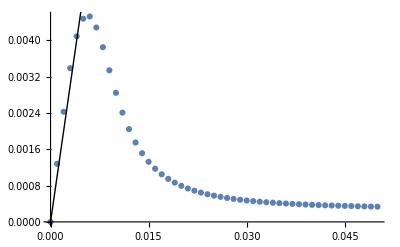

```mathematica
dynfig=ListPlot[poputable,PlotRange->All,Epilog->Line[{{0,0},{1,1}}]]
```

```mathematica
Atemp=PopuEquilibrium[mystrat,EnvIniNormal,defpara]
```

0.00418496

```mathematica
DoStepPrint[Atemp,mystrat,EnvIniNormal,defpara]
```

Snow 3.15937 at time 87 => mortality 0.00479789

Adults:0.00383626 Pile 1122.75

Snow 0.600719 at time 170 => mortality 0.0028764

Adults 0.0035307 Pile:4383.68 survival: 0.57314

Juveniles 0.00417133 Pile:3392.36 survival: 0.51815

Resource. R(0)=3 ,R(tau)=34.2603 R(end)=54.4196

0.00418496

```mathematica
RsearchCondition[Atemp,mystrat,EnvIniNormal,defpara]
```

1.

```mathematica
DoStep[Atemp,mystrat,EnvIniNormal,defpara]
```

0.00418496

```mathematica
GradientDoStep[{mystrat,Atemp,EnvIniNormal},defpara]
```

0.0000270826

### Plotting

```mathematica
Atemp
```

0.00418496

Snow 3.15937 at time 87 => mortality 0.00479789

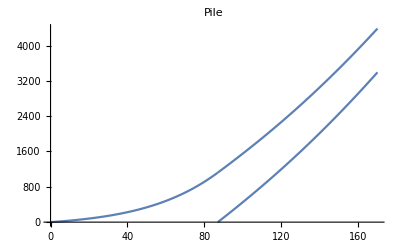

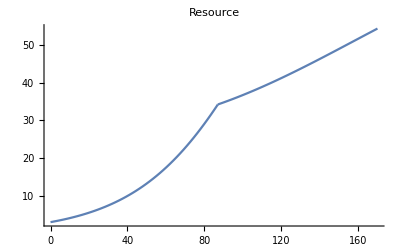

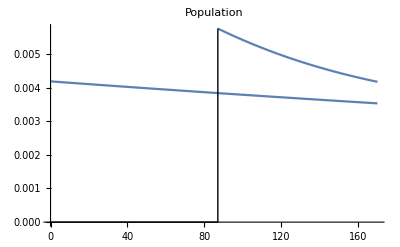

Snow 0.600719 at time 170 => mortality 0.0028764

Adults 0.0035307 Pile:4383.68 survival: 0.57314

Juveniles 0.00417133 Pile:3392.36 survival: 0.51815

Resource. R(0)=3 ,R(tau)=34.2603 R(end)=54.4196

0.00418496

```mathematica
DoStepPlot[Atemp,mystrat,EnvIniNormal,defpara]
```

### Equilibria and fitness gradient

```mathematica
tasat=Table[{tau,PopuEquilibrium[tau,EnvIniNormal,defpara],EnvIniNormal},{tau,0,seasonT,seasonT/100}];
```

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

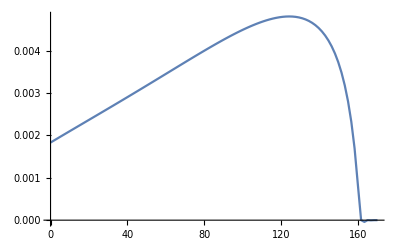

```mathematica
ListPlot[Koord[tasat],Joined->True,PlotRange->All]
```

```mathematica
gradlista2=Map[{#[[1]],GradientDoStep[#,defpara]}&,tasat];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

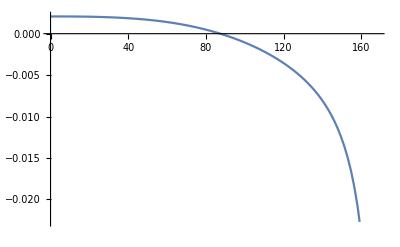

```mathematica
gradkuva=ListPlot[{gradlista2},Joined->True]
```

```mathematica
GradientFinder[{mystrat,EnvIniNormal},defpara]
```

0.0000270826

```mathematica
FindRoot[GradientFinder[{strat,EnvIniNormal},defpara]==0,{strat,seasonT/2}]
```

{strat→87.3757}

```mathematica
mysing=SingularTime[EnvIniNormal,defpara]
```

87.3757

```mathematica
Snow[EnvIniNormal,mysing,defpara]
```

3.13572

```mathematica
singtable=Table[{Env,SingularTime[Env,defpara]},{Env,10,22}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{10,80.6114},{11,81.8046},{12,82.8624},{13,83.8084},{14,84.6606},{15,85.4331},{16,86.1372},{17,86.7822},{18,87.3757},{19,87.9237},{20,88.4317},{21,88.9041},{22,89.3446}}

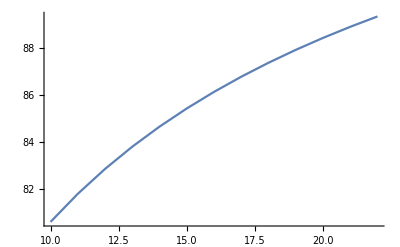

```mathematica
ListPlot[singtable,Joined->True]
```

```mathematica
DatePlus["March 15,2021",89]
```

Sat 12 Jun 2021 00:00:00

```mathematica
GradientRandomStep[{grad_,A_},tau_,{EnvAver_,EnvDev_}]
```

```mathematica
GradientFullStep[{mystrat,Atemp,EnvIniNormal},defpara]
```

{0.0000270826,0.00418496}

```mathematica
GradientRandomStep[{0,Atemp},mystrat,{EnvIniNormal,5},defpara]
```

{-0.0000175081,0.00420056}

```mathematica
haku=Nest[GradientRandomStep[#,mystrat,{EnvIniNormal,5},defpara]&,{0,Atemp},50]
```

{0.0000321935,0.00417532}

```mathematica
hakulista=NestList[GradientRandomStep[#,mystrat,{EnvIniNormal,5},defpara]&,haku,50];
```

```mathematica
Mean[Map[First,hakulista]]
```

0.0000238207

```mathematica
GradientRandomFinder[mystrat,{EnvIniNormal,5},{50,50},defpara]
```

0.000018806

```mathematica
randGradT=Table[{tau,GradientRandomFinder[tau,{EnvIniNormal,5},{50,50},defpara]},{tau,0,seasonT,seasonT/100}];
```

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
randGradT2=Table[{tau,GradientRandomFinder[tau,{EnvIniNormal,15},{50,50},defpara]},{tau,0,seasonT,seasonT/100}];
```

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

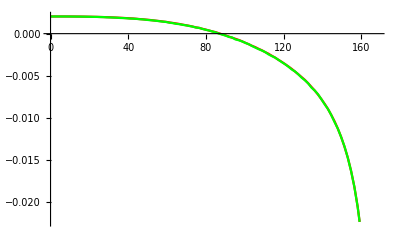

```mathematica
randKuva=ListPlot[{randGradT,randGradT2},Joined->True,PlotStyle->{Red,Green}]
```

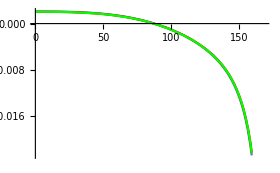

```mathematica
Show[gradkuva,randKuva]
```

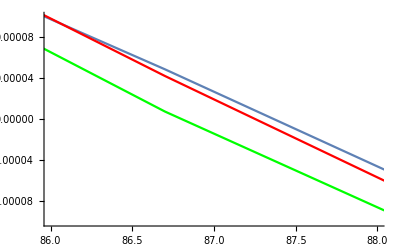

```mathematica
Show[gradkuva,randKuva,PlotRange->{{86,88},{-0.0001,0.0001}}]
```

### Random environment

```mathematica
searchlow=80;
searchhigh=94;
```

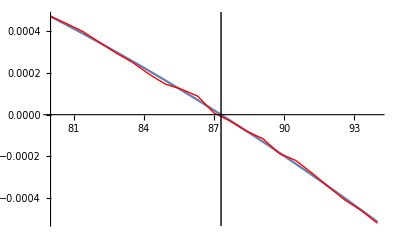

87.3014

```mathematica
RandSingularSearch[{searchlow,searchhigh,20},{EnvIniNormal,5},{10,50},defpara,1]
```

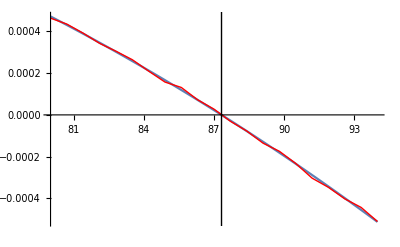

87.3217

```mathematica
RandSingularSearch[{searchlow,searchhigh,20},{EnvIniNormal,5},{10,50},1]
```

```mathematica
searchlow=84;
searchhigh=88;
```

```mathematica
Print[Now]
```

Sat 17 Jul 2021 12:23:38GMT+3.

```mathematica
Print[Now];singlist=Table[{dev,dev^2/12,RandSingularSearch[{searchlow,searchhigh,20},{EnvIniNormal,dev},{10,100},defpara,0]},{dev,0,20}];
Print[Now];
```

Sun 18 Jul 2021 00:39:50GMT+3.

Sun 18 Jul 2021 00:42:03GMT+3.

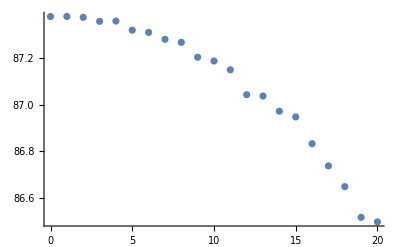

```mathematica
ListPlot[Map[{#[[1]],#[[3]]}&,singlist2]]
```

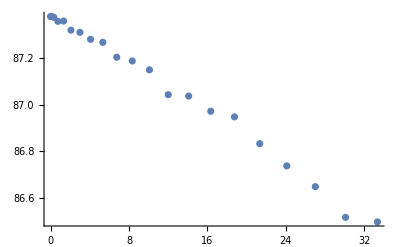

```mathematica
ListPlot[Map[{#[[2]],#[[3]]}&,singlist2]]
```

### Threshold strategy & random environment

```mathematica
GradientThresholdRandomFinder[3,{EnvIniNormal,5},{50,50},defpara]
```

0.00266806

```mathematica
PrintTemporary
```

```mathematica
randGradThresholdT=Table[{thre,GradientThresholdRandomFinder[thre,{EnvIniNormal,5},{50,50},defpara]},{thre,1,5,0.1}];
```

```mathematica
randGradThresholdT
```

{{0.5,-26.0107},{1.,0.4813},{1.5,0.135532},{2.,0.0544479},{2.5,0.0173088},{3.,0.00241678},{3.5,-0.00559889},{4.,-0.00937903},{4.5,-0.0116147},{5.,-0.0121812}}

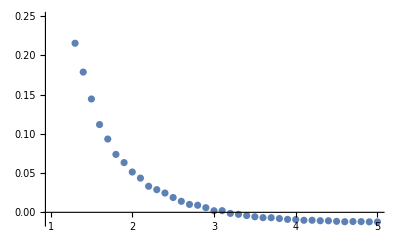

```mathematica
ListPlot[randGradThresholdT]
```

Fri 23 Jul 2021 13:34:39GMT+3.

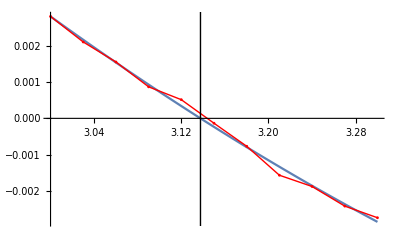

Fri 23 Jul 2021 13:34:55GMT+3.

3.13759

```mathematica
Print[Now];
koesing=RandSingularThresholdSearch[{3,3.3,10},{EnvIniNormal,5},{50,500},defpara,2];
Print[Now];koesing
```

```mathematica
Tlow=3.0;Thigh=3.3;
```

```mathematica
Print[Now];singlistThresholdTest2=Table[{dev,dev^2/12,RandSingularThresholdSearch[{Tlow,Thigh,20},{EnvIniNormal,dev},{100,100},defpara,0]},{dev,0,20,2}];
Print[Now];
```

Sat 24 Jul 2021 09:05:30GMT+3.

Sat 24 Jul 2021 09:08:10GMT+3.

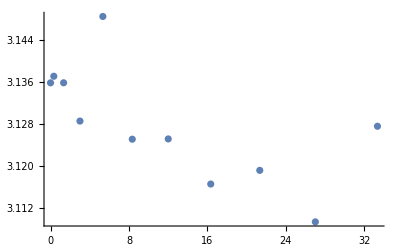

```mathematica
PartListPlot[singlistThresholdTest2,2]
```

```mathematica
Tlow=3.1;Thigh=3.15;
```

```mathematica
(* step 100, tablestep 2 about 2 min 20 sec
  step 1000, tablestep 2 about 11 min *)
```

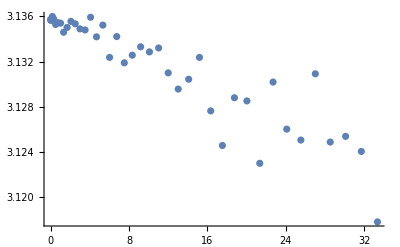

```mathematica
PartListPlot[singlistThreshold,2]
```

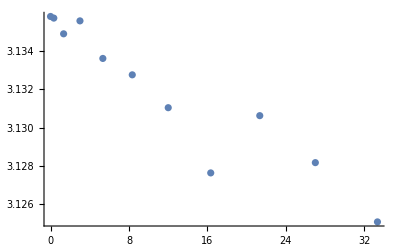

```mathematica
PartListPlot[singlistThreshold,2]
```

```mathematica
EnvIniNormal
```

18

```mathematica
TimeAnalysis[3,{EnvIniNormal,5},defpara,1]
```

Time bounds {82.1114,96.0906} Average=89.4263 Middle=89.588

Probabilities {0,1.,0} 1.

{89.4263,82.1114,96.0906}

```mathematica
TimeAnalysis[3,{EnvIniNormal,35.0},defpara,1]
```

Time bounds {0,123.546} Average=78.8824 Middle=89.588

Probabilities {0.0714286,0.928571,0} 1.

{78.8824,0,123.546}

```mathematica
Exp[seasonT*ParaDecayDelta[defpara]]*3
```

89.8923

```mathematica
TimeAnalysis[3,{80,35},defpara,1]
```

Time bounds {151.828,170} Average=163.319 Middle=164.171

Probabilities {0,0.782637,0.217363} 1.

{163.319,151.828,170}

```mathematica
singlistThreshold
```

{{0,0,3.13578},{2,1/3,3.13733},{4,4/3,3.13733},{6,3,3.13439},{8,16/3,3.14137},{10,25/3,3.13518},{12,12,3.12581},{14,49/3,3.13018},{16,64/3,3.12},{18,27,3.12445},{20,100/3,3.13728}}

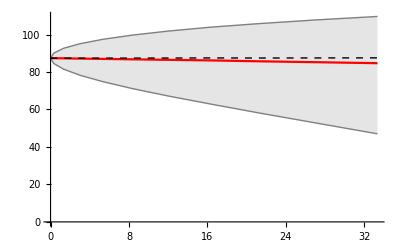
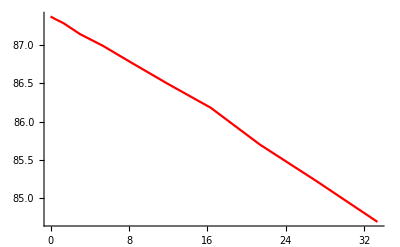

```mathematica
thplot=TimePlot[singlistThreshold,EnvIniNormal,defpara,2]
```

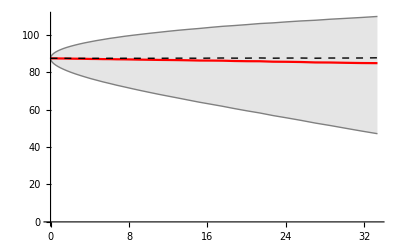
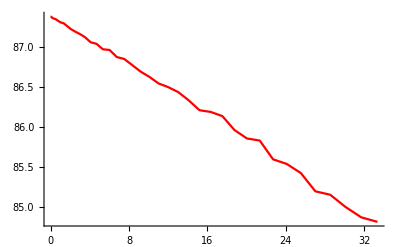

```mathematica
thplot=TimePlot[singlistThreshold,EnvIniNormal,defpara,2]
```

## Investigating the slope

### How the gradient changes wrt environment

```mathematica
singpopu=PopuEquilibrium[mysing,EnvIniNormal,defpara]
```

0.00419456

```mathematica
grderi=GradientDeri[{mysing,singpopu,EnvIniNormal},defpara,2]
```

RJ/(RJ+RA)=0.5165

Current snow=3.13572, K=1

-2.21588×10^-6

```mathematica
Print[Now]; (* Aika: 1000=> 1 min, 10000 => 8.5 min *) gradAtSingList=Table[{dev,dev^2/12,GradientRandomFinder[mysing,{EnvIniNormal,dev},{10,10000},defpara]},{dev,0,20}];
Print[Now];
```

Sat 17 Jul 2021 13:36:21GMT+3.

Sat 17 Jul 2021 13:44:59GMT+3.

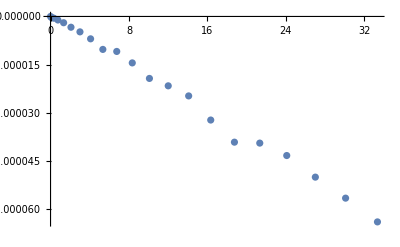

```mathematica
gradderikuva=PartListPlot[gradAtSingList,2]
```

```mathematica
Fit[PartList[gradAtSingList,2],{1,x},x]
```

4.82261×10^-7-1.90596×10^-6 x

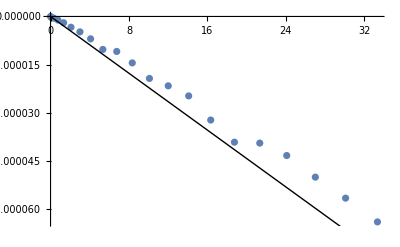

```mathematica
Show[gradderikuva,Epilog->Line[{{0,0},{35,35*grderi}}]]
```

### How the gradient changes wrt strategy

```mathematica
GradStratList=Table[{tau,GradientFinder[{tau,EnvIniNormal}]},{tau,84,90,0.1}];
```

```mathematica
grf=Fit[GradStratList,{1,x,x^2},x]
```

-0.000407289+0.0000817718 x-8.82517×10^-7 x^2

```mathematica
grf2=Fit[GradStratList,{1,(x-mysing),(x-mysing)^2},x]
```

-9.04817×10^-9-0.0000724493 (-87.3757+x)-8.82517×10^-7 (-87.3757+x)^2

```mathematica
stratderi=D[grf,x]/. x->mysing
```

-0.0000724493

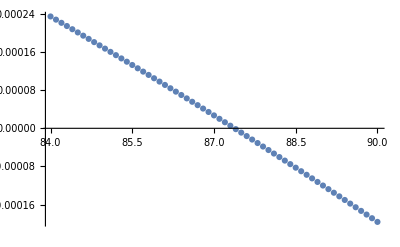

```mathematica
ListPlot[GradStratList]
```

### How the singular strategy changes wrt environment

```mathematica
singderi=-grderi/stratderi
```

-0.0305853

RJ/(RJ+RA)=0.5165

Current snow=3.13572, K=1

Gradient derivative wrt environment-2.21588×10^-6

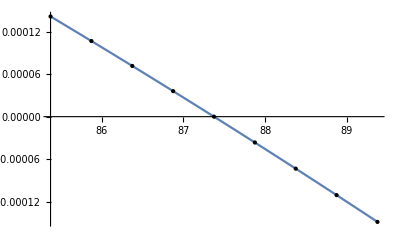

Gradient derivative wrt strategy-0.0000724393

{87.3757,0.00419456,-0.0305895}

{87.3757,0.00419456,-0.0305895}

```mathematica
SensitivityAnalysis[EnvIniNormal,defpara,3]
```

```mathematica
mysing
```

87.3757

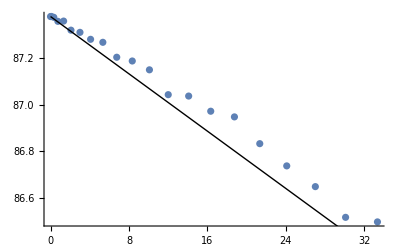

```mathematica
Show[PartListPlot[ singlist2,2],Epilog->Line[{{0,mysing},{35,mysing+singderi*35}}]]
```

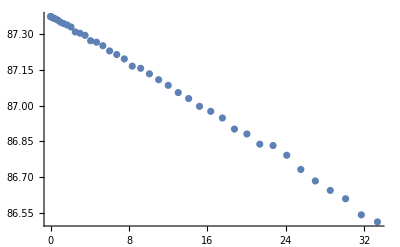

```mathematica
PartListPlot[ singlist3,2]
```

### How sensitivity to the variance changes when parameters are changed?

```mathematica
defpara
```

{0.02,0.001,0.001,0.005,1}

```mathematica
senstaulu=Table[{K,SensitivityAnalysis[EnvIniNormal,{0.02,0.001,0.001,0.005,K},1]},{K,0.2,4,0.2}];
```

{98.3746,0.00399923,-0.0121727}

{94.9202,0.0040814,-0.0196677}

{92.035,0.00413443,-0.0246408}

{89.5539,0.00417008,-0.0281021}

{87.3757,0.00419456,-0.0305895}

{85.4331,0.0042115,-0.0324164}

{83.6794,0.00422315,-0.0337772}

{82.0807,0.00423096,-0.0347991}

{80.6114,0.00423593,-0.0355683}

{79.252,0.00423875,-0.0361453}

{77.9871,0.00423994,-0.0365738}

{76.8041,0.00423985,-0.0368857}

{75.6932,0.00423876,-0.0371054}

{74.6459,0.00423688,-0.0372512}

{73.6554,0.00423437,-0.0373373}

{72.7157,0.00423137,-0.0373749}

{71.822,0.00422797,-0.0373729}

{70.9698,0.00422425,-0.0373383}

{70.1555,0.00422028,-0.037277}

{69.3758,0.0042161,-0.0371936}

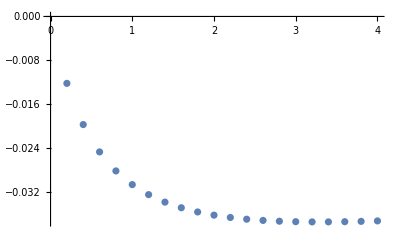

```mathematica
ListPlot[Map[{#[[1]],#[[2]][[3]]}&,senstaulu]]
```

```mathematica
senstaulu2=Table[{JED,SensitivityAnalysis[EnvIniNormal,{0.02,0.001,0.001,JED,2},1]},{JED,0.001,0.01,0.001}];
```

{26.901,0.00362337,-0.0221226}

{48.8082,0.00392536,-0.0290141}

{62.162,0.00408733,-0.0328084}

{71.7786,0.00418279,-0.0349678}

{79.252,0.00423875,-0.0361453}

{85.3254,0.00426864,-0.0366999}

{90.4104,0.00428017,-0.0368477}

{94.7605,0.00427823,-0.0367255}

{98.5435,0.00426609,-0.0364229}

{101.876,0.00424602,-0.0360001}

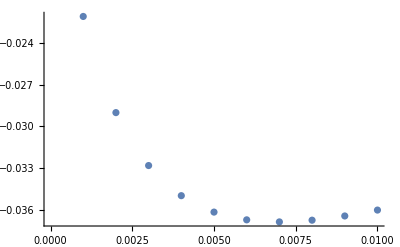

```mathematica
ListPlot[Map[{#[[1]],#[[2]][[3]]}&,senstaulu2]]
```

## Stored calculations

```mathematica
(* 1000 *)
singlist2={{0,0,87.37559845621891},{1,1/12,87.37595507838459},{2,1/3,87.37224294926881},{3,3/4,87.35511831379809},{4,4/3,87.3562549479068},{5,25/12,87.3174798397868},{6,3,87.30812755147409},{7,49/12,87.27840569381912},{8,16/3,87.26561959332211},{9,27/4,87.20190288322303},{10,25/3,87.1859032194438},{11,121/12,87.1482158174251},{12,12,87.04217092751642},{13,169/12,87.03627157359297},{14,49/3,86.97153682184549},{15,75/4,86.9473373197725},{16,64/3,86.83310617841852},{17,289/12,86.7382166059133},{18,27,86.6497378629001},{19,361/12,86.51867893725745},{20,100/3,86.49921149281364}};
```

```mathematica
singlist3={{0.,0.,87.3755984561652},{0.5,0.020833333333333332,87.37480152780674},{1.,0.08333333333333333,87.37361037218952},{1.5,0.1875,87.37098549562168},{2.,0.3333333333333333,87.36765880632545},{2.5,0.5208333333333333,87.36489787549496},{3.,0.75,87.3596562754844},{3.5,1.0208333333333333,87.35148054520866},{4.,1.3333333333333333,87.34577305613651},{4.5,1.6875,87.3398466389426},{5.,2.083333333333333,87.33149342241188},{5.5,2.520833333333333,87.31058196012086},{6.,3.,87.3049980846895},{6.5,3.520833333333333,87.29611124419556},{7.,4.083333333333333,87.27359888619107},{7.5,4.6875,87.26724536248102},{8.,5.333333333333333,87.25262652774705},{8.5,6.020833333333333,87.23071791231838},{9.,6.75,87.21538385704973},{9.5,7.520833333333333,87.19700059561993},{10.,8.333333333333332,87.16647917241058},{10.5,9.1875,87.1575786427692},{11.,10.083333333333332,87.13422697213694},{11.5,11.020833333333332,87.1094329339511},{12.,12.,87.08571997530919},{12.5,13.020833333333332,87.0553727634311},{13.,14.083333333333332,87.03031186933741},{13.5,15.1875,86.99742245694792},{14.,16.333333333333332,86.97628878184076},{14.5,17.520833333333332,86.94842975853784},{15.,18.75,86.90177773505097},{15.5,20.020833333333332,86.88114525792446},{16.,21.333333333333332,86.8381709446851},{16.5,22.6875,86.83248516028169},{17.,24.083333333333332,86.79148726024219},{17.5,25.520833333333332,86.73175941553394},{18.,27.,86.68340909168066},{18.5,28.520833333333332,86.64373825258204},{19.,30.083333333333332,86.6085544750679},{19.5,31.6875,86.5408120632245},{20.,33.33333333333333,86.51121096317314}};
```

```mathematica
(* 10 000 *)
gradAtSingList={{0,0,2.5382277520757456*^-12},{1,1/12,-3.201689088530031*^-7},{2,1/3,-5.398525681371698*^-7},{3,3/4,-1.1008740395124656*^-6},{4,4/3,-1.9579890768591264*^-6},{5,25/12,-3.359573554968304*^-6},{6,3,-4.805041536402739*^-6},{7,49/12,-6.97636566333489*^-6},{8,16/3,-0.000010278098371642592},{9,27/4,-0.000010912861173229461},{10,25/3,-0.000014483692939869498},{11,121/12,-0.000019329905348409503},{12,12,-0.000021634437741587173},{13,169/12,-0.000024780786406142086},{14,49/3,-0.000032304435121144113},{15,75/4,-0.00003920734838585797},{16,64/3,-0.000039497139710238134},{17,289/12,-0.00004337471068216953},{18,27,-0.00005011195593759498},{19,361/12,-0.00005666675315066588},{20,100/3,-0.0000640738247556556}};
```

```mathematica
singlistThresholdSmall={{0,0,3.1357791534197768},{2,1/3,3.135693502356891},{4,4/3,3.1348758762884494},{6,3,3.1355494779380297},{8,16/3,3.1335945198122555},{10,25/3,3.1327420695467554},{12,12,3.131031678610758},{14,49/3,3.1276382617275402},{16,64/3,3.1306175531533804},{18,27,3.1281726053611614},{20,100/3,3.125088995139466}}
```

```mathematica
singlistThreshold={{0.,0.,3.1357179544005676},{0.5,0.020833333333333332,3.13566352083387},{1.,0.08333333333333333,3.1356414655907017},{1.5,0.1875,3.1359851425122303},{2.,0.3333333333333333,3.135753350952343},{2.5,0.5208333333333333,3.1352764675570604},{3.,0.75,3.1354365614097266},{3.5,1.0208333333333333,3.1353920140734237},{4.,1.3333333333333333,3.134588830375576},{4.5,1.6875,3.1350143298939472},{5.,2.083333333333333,3.1355525235477395},{5.5,2.520833333333333,3.1353332731247705},{6.,3.,3.1348868446045697},{6.5,3.520833333333333,3.1347940240595205},{7.,4.083333333333333,3.1359164295813393},{7.5,4.6875,3.1341839741407584},{8.,5.333333333333333,3.135220284716056},{8.5,6.020833333333333,3.132367638628269},{9.,6.75,3.134208129319353},{9.5,7.520833333333333,3.1318878809780983},{10.,8.333333333333332,3.1325630268283198},{10.5,9.1875,3.133300965091728},{11.,10.083333333333332,3.1328534773478434},{11.5,11.020833333333332,3.133200662414259},{12.,12.,3.1309973381396357},{12.5,13.020833333333332,3.1295692580012737},{13.,14.083333333333332,3.130434686749},{13.5,15.1875,3.132367472633875},{14.,16.333333333333332,3.1276404113679614},{14.5,17.520833333333332,3.124583372039965},{15.,18.75,3.128802595407806},{15.5,20.020833333333332,3.1285195915442925},{16.,21.333333333333332,3.123005672726687},{16.5,22.6875,3.1301868863517948},{17.,24.083333333333332,3.1260271930654304},{17.5,25.520833333333332,3.125062297217506},{18.,27.,3.1309153927113575},{18.5,28.520833333333332,3.124886202927781},{19.,30.083333333333332,3.1253898382700314},{19.5,31.6875,3.1240552781998403},{20.,33.33333333333333,3.1178290672256916}};
```

## “Final” plots

### Panel A - environmental cue

```mathematica
PartListPlot[singlistThreshold,2]
```

-Graphics-

### Panel B - environmental cue

```mathematica
thplot=TimePlot[singlistThreshold,EnvIniNormal,defpara,2]
```

{-Graphics-,-Graphics-}

### Panel C - timing cue

```mathematica
singderi=-0.03058527842380302
```

-0.0305853

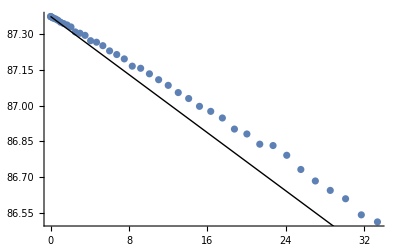

```mathematica
timefig=Show[PartListPlot[ singlist3,2],Epilog->Line[{{0,mysing},{35,mysing+singderi*35}}]]
```

### Panel D - both cues together

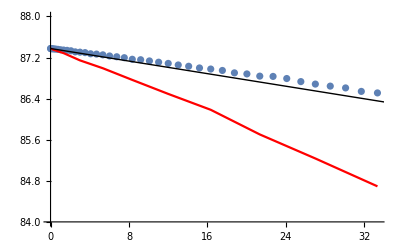

```mathematica
Show[timefig,thplot[[2]],PlotRange->{84,88},AxesOrigin->{0,84}]
```

## Commands for the lengthy calculations (no need to run again)

### Timing cue

```mathematica
searchlow=84;
searchhigh=88;
```

```mathematica
(* Time needed  
   100: 2min40 sec
  1000: 22 min  
    10 000 (step 0.5): about 6 hours
 *)
```

```mathematica
Print[Now];(* 22 minutes running time *)singlist2=Table[{dev,dev^2/12,RandSingularSearch[{searchlow,searchhigh,20},{EnvIniNormal,dev},{10,1000},defpara,0]},{dev,0,20}];
Print[Now];
```

Sat 17 Jul 2021 12:31:15GMT+3.

Sat 17 Jul 2021 12:53:21GMT+3.

```mathematica
Print[Now]; (* 6 hours running time *)singlist3=Table[{dev,dev^2/12,RandSingularSearch[{searchlow,searchhigh,20},{EnvIniNormal,dev},{100,10000},defpara,0]},{dev,0,20,0.5}];
Print[Now];
```

Sun 18 Jul 2021 00:49:17GMT+3.

Sun 18 Jul 2021 06:55:41GMT+3.

### Environmental cue

```mathematica
Tlow=3.0;Thigh=3.3;
```

```mathematica
Print[Now]; (* running time with these parameters unknown, around 6 hours probably *)singlistThreshold=Table[{dev,dev^2/12,RandSingularThresholdSearch[{Tlow,Thigh,20},{EnvIniNormal,dev},{100,10000},defpara,0]},{dev,0,20,0.5}];
Print[Now];
```